```mathematica
(* Constructing Lists using Table*)
threes = Table[3,{5}]
alist = Table[i,{i,8}]
alolon = Table[ 3*(i-1)+j,{i,4},{j,3}]
```

{3,3,3,3,3}

{1,2,3,4,5,6,7,8}

{{1,2,3},{4,5,6},{7,8,9},{10,11,12}}

```mathematica
(* Single Element Selection *)
alist[[3]]
{4,52,3,6}[[2]]
alolon[[4,2]]
```

3

52

11

```mathematica
(* Multi Element Selection *)
alist[[{1,3,5}]]
alist[[{3,5,1}]]
{4,52,3,6}[[Table[2,{10}]]]
```

{1,3,5}

{3,5,1}

{52,52,52,52,52,52,52,52,52,52}

```mathematica
(* Multi Element Selection with Spans *)
blist = Table[20-i,{i,1,20}]
blist[[1;;5]]
blist[[6;;]]
blist[[;;10]]
blist[[;;]]
blist[[20;;1;;-1]]
blist[[1;;20;;3]]
```

{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}

{19,18,17,16,15}

{14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}

{19,18,17,16,15,14,13,12,11,10}

{19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1,0}

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

{19,16,13,10,7,4,1}

```mathematica
(* Selecting from 2D/Table like Lists *)
alolon[[2]]
alolon[[;;,1]]
alolon[[1;;2,{1,3}]]
```

{4,5,6}

{1,4,7,10}

{{1,3},{4,6}}

```mathematica
mytab=Table[10*i+j,{i,0,19},{j,0,9}]
```

{{0,1,2,3,4,5,6,7,8,9},{10,11,12,13,14,15,16,17,18,19},{20,21,22,23,24,25,26,27,28,29},{30,31,32,33,34,35,36,37,38,39},{40,41,42,43,44,45,46,47,48,49},{50,51,52,53,54,55,56,57,58,59},{60,61,62,63,64,65,66,67,68,69},{70,71,72,73,74,75,76,77,78,79},{80,81,82,83,84,85,86,87,88,89},{90,91,92,93,94,95,96,97,98,99},{100,101,102,103,104,105,106,107,108,109},{110,111,112,113,114,115,116,117,118,119},{120,121,122,123,124,125,126,127,128,129},{130,131,132,133,134,135,136,137,138,139},{140,141,142,143,144,145,146,147,148,149},{150,151,152,153,154,155,156,157,158,159},{160,161,162,163,164,165,166,167,168,169},{170,171,172,173,174,175,176,177,178,179},{180,181,182,183,184,185,186,187,188,189},{190,191,192,193,194,195,196,197,198,199}}

```mathematica
tabview= 
Labeled[TableForm[mytab,TableHeadings->
{Table[i,{i,20}],{"a","b","c","d","e","f","g","h","i","j"}}],
"Table 1: Some data showing some relationship",Spacings->{Automatic,2}]
```

| a | b | c | d | e | f | g | h | i | j
1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
2 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19
3 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29
4 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39
5 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49
6 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59
7 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69
8 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79
9 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89
10 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99
11 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109
12 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119
13 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129
14 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139
15 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149
16 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159
17 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169
18 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179
19 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189
20 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199Table 1: Some data showing some relationship

```mathematica
Export["TimesTable.svg",tabview]
```

TimesTable.svg

```mathematica
(*Random Table *)
randtab = RandomVariate[NormalDistribution[],{20,10}];
TableForm[randtab]
```

-1.57121 | -1.02148 | -0.130759 | 0.274093 | -0.532927 | -0.99625 | -0.823049 | -0.695356 | -0.66286 | -1.0101
0.452126 | 0.179384 | -0.0454249 | -0.368802 | 1.30727 | -1.52352 | 0.0820726 | -0.663264 | -0.0651243 | -0.154424
-0.023975 | -0.676653 | 0.250949 | 1.15522 | -0.639743 | -2.20802 | -0.67507 | 1.3458 | -0.647689 | 0.0484314
-0.45031 | 0.104165 | -0.238318 | 0.897136 | 1.34434 | -0.356061 | -0.105148 | -0.989157 | -0.153331 | 0.94613
-1.17317 | 1.6401 | 0.808361 | -0.255507 | 1.34099 | 2.47008 | 0.671424 | 0.138071 | 1.09329 | 0.0560871
0.857629 | 1.29769 | -1.86916 | 1.2468 | 0.0314892 | 1.22839 | -0.461957 | -0.175254 | -1.49458 | 0.794416
1.01226 | 0.553244 | -0.0215323 | -1.02109 | -0.589726 | -0.241244 | -0.520784 | 0.084405 | 0.528483 | 0.265473
0.937951 | 0.242369 | -0.211933 | -1.10578 | 1.10876 | -1.00792 | 0.409086 | 0.0610006 | 0.472319 | 1.59536
-0.401638 | -1.55363 | -0.788152 | -0.782204 | 0.257527 | -0.670066 | 0.780606 | 0.422952 | 1.37136 | -1.40276
-0.190082 | 0.388814 | -0.783518 | 0.505175 | -0.676368 | 0.151727 | -0.671553 | -0.46672 | -0.740792 | 0.175592
-0.600354 | 0.584071 | -0.594973 | -0.404814 | 1.44838 | -1.68118 | 2.77094 | -0.434756 | -1.2494 | -1.04362
-0.269957 | 1.30696 | 1.661 | -1.25567 | 1.78107 | 0.673416 | -0.00346763 | -0.956721 | -1.07043 | 0.775383
0.385734 | 1.24055 | -0.677289 | 1.29322 | -0.193259 | -0.774225 | -0.422593 | 2.03736 | 0.302962 | 1.11604
1.22649 | -1.47036 | -0.0449613 | -0.338048 | -1.25446 | 0.237887 | 0.287391 | -0.504436 | 0.0910657 | -0.121884
1.83844 | 0.366861 | -0.975073 | -0.602164 | -0.334898 | 1.73454 | 0.128973 | 0.188726 | 0.316373 | -1.36524
-0.966341 | -1.13326 | 0.566623 | -1.14846 | 0.525049 | 0.387825 | -0.176794 | -0.0354002 | 0.835267 | -0.124005
-0.438646 | -0.724411 | -0.5868 | -0.214308 | -2.82447 | -0.706743 | -1.226 | -0.85745 | 0.220357 | 0.877992
0.794501 | 0.0495914 | 1.721 | 0.274954 | -0.994501 | -0.361265 | 0.814222 | 1.02387 | -1.13967 | 2.06717
-1.44312 | -0.772524 | 1.06805 | -1.19014 | -0.402683 | -0.833532 | -0.805159 | -0.212206 | 0.0836396 | -0.289875
1.10668 | -1.01624 | -1.7007 | 0.0459738 | 0.419956 | -1.55502 | -0.424803 | -0.456382 | 1.09544 | 0.280995

```mathematica
(* Min/max for the whole table, by row, then by Column *)
Min[randtab]
Max[randtab]
Map[Min,randtab]
Map[Max,randtab]
Map[Min,Transpose[randtab]]
Map[Max,Transpose[randtab]]
```

-2.82447

2.77094

{-1.57121,-1.52352,-2.20802,-0.989157,-1.17317,-1.86916,-1.02109,-1.10578,-1.55363,-0.783518,-1.68118,-1.25567,-0.774225,-1.47036,-1.36524,-1.14846,-2.82447,-1.13967,-1.44312,-1.7007}

{0.274093,1.30727,1.3458,1.34434,2.47008,1.29769,1.01226,1.59536,1.37136,0.505175,2.77094,1.78107,2.03736,1.22649,1.83844,0.835267,0.877992,2.06717,1.06805,1.10668}

{-1.57121,-1.55363,-1.86916,-1.25567,-2.82447,-2.20802,-1.226,-0.989157,-1.49458,-1.40276}

{1.83844,1.6401,1.721,1.29322,1.78107,2.47008,2.77094,2.03736,1.37136,2.06717}

```mathematica
(* Mean by Row and Column *)
```

```mathematica
Mean[Transpose[randtab]]
Mean[randtab]
```

{-0.71699,-0.07997,-0.207074,0.0999449,0.678973,0.145546,0.00494873,0.250121,-0.2766,-0.230773,-0.12057,0.264158,0.43085,-0.189132,0.129654,-0.126949,-0.648048,0.424987,-0.479755,-0.22041}

{0.0541499,-0.0207387,-0.129631,-0.14972,0.0560902,-0.301559,-0.0185831,-0.0572459,-0.0406659,0.174359}

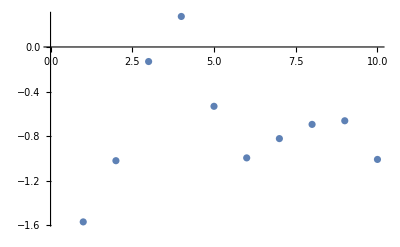

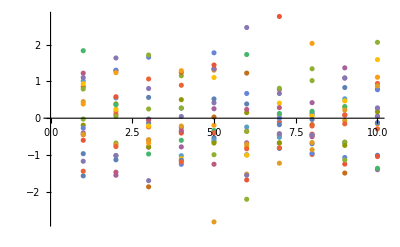

```mathematica
ListPlot[randtab[[1]]]
ListPlot[randtab]
```

```mathematica
xs=Table[10*i,{i,10}]
```

{10,20,30,40,50,60,70,80,90,100}

```mathematica
Transpose[{xs,randtab[[1]]}]
```

{{10,-1.57121},{20,-1.02148},{30,-0.130759},{40,0.274093},{50,-0.532927},{60,-0.99625},{70,-0.823049},{80,-0.695356},{90,-0.66286},{100,-1.0101}}

```mathematica
Zip[xs_,ys_]:=Transpose[{xs,ys}]
```

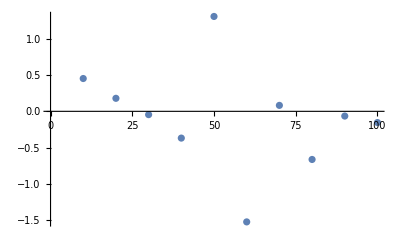

```mathematica
points=Zip[xs,randtab[[2]]];
ListPlot[points]
```

```mathematica
MakePoints[xs_,ytab_] :=
Map[Zip[Table[xs[[#]],{i,Length[ytab[[#]]]}],ytab[[#]] ]&,Table[i,{i,Length[ytab]}]]
```

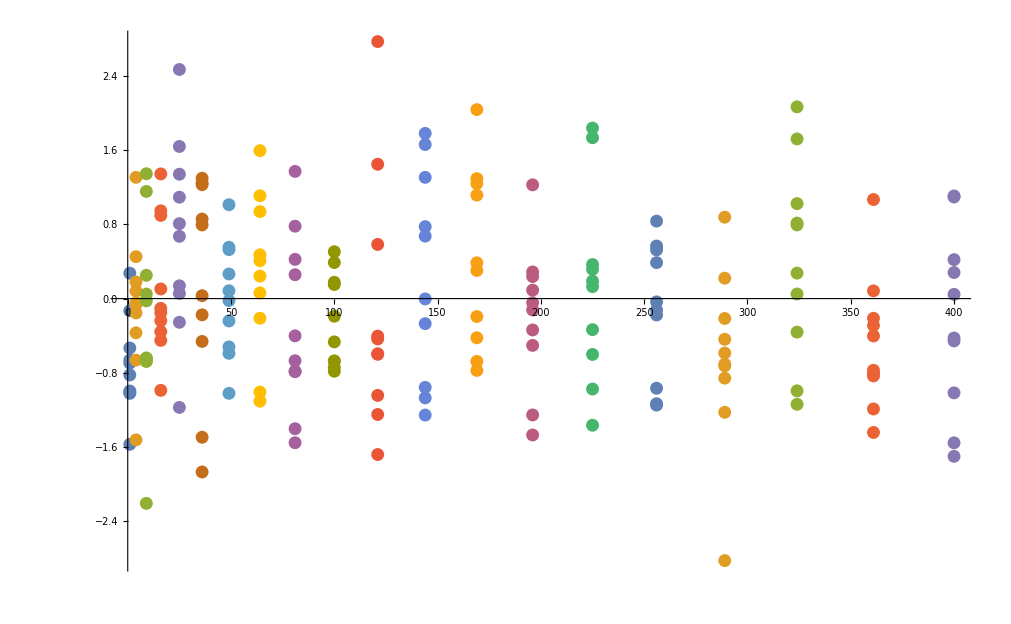

```mathematica
morepoints = MakePoints[Table[i^2,{i,Length[randtab]}],randtab];
ListPlot[morepoints]
```

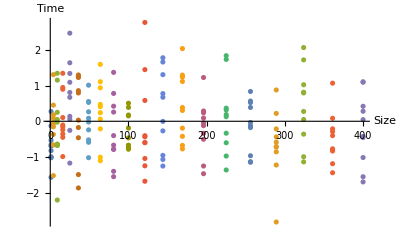

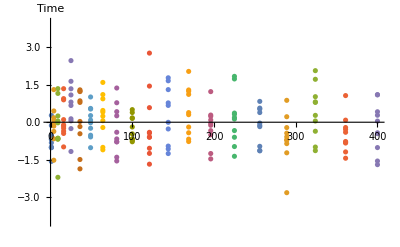

```mathematica
ListPlot[morepoints,AxesLabel->{"Size","Time"},PlotRange->All]
ListPlot[morepoints,AxesLabel->{None,"Time"},PlotRange->{-4,4}]
```

```mathematica
mypoints=Labeled[ListPlot[morepoints,AxesLabel->{"Size","Time"},PlotRange->All],"Figure 2: Size and Time...",Spacings->{Automatic,2}]
Export["datapoints.svg",mypoints]
```